```mathematica
n=100; m=1;
```

```mathematica
(*Este codigo lo puedo hacer con distincion de colores para los cuñados y hermanos tambien, en caso de ser necesario *)
```

```mathematica
kaux={}; cc={}; ncct=0; nccr=0; x=0; lncct={}; lnccr={}; lvd={}; lscct={}; lsccr={};  scct=ConstantArray[0, n+1]; sccr=ConstantArray[0, n+1]; Do[kaux={};cc={}; x=0;  {spression=ToExpression[StringSplit[ReadLine["D:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 6 - Maestria 1\\Trabajo Especial\\Net_Generation\\n0143.txt"]]]; While[spression≠ {0,0}, {kaux=Join[kaux, {spression}], lscct={}, lsccr={}, spression=ToExpression[StringSplit[ReadLine["D:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 6 - Maestria 1\\Trabajo Especial\\Net_Generation\\n0143.txt"]]]}],t=Table[kaux[[i,1]]<->kaux[[i,2]], {i, 1, Length[kaux]}], r=t, Do[{r1=RandomInteger[{1,Length[t] }], r2=RandomInteger[{1,Length[t] }], help=r[[r1, 2]], r[[r1, 2]]=r[[r2,2]], r[[r2, 2]]=help},n]} , m];
```

```mathematica
(*alfa=0.7    kinship*)
```

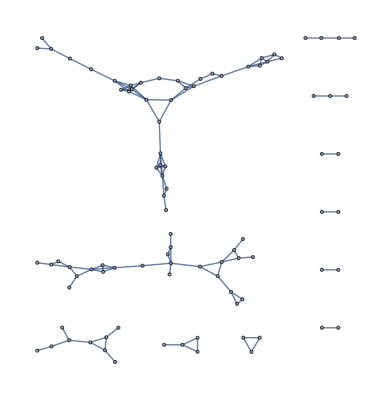

```mathematica
Graph[t]
```

```mathematica
(*alfa=0.7    random*)
```

```mathematica
Graph[r]
```

-Graphics-

```mathematica
kaux={}; cc={}; ncct=0; nccr=0; x=0; lncct={}; lnccr={}; lvd={}; lscct={}; lsccr={};  scct=ConstantArray[0, n+1]; sccr=ConstantArray[0, n+1]; Do[kaux={};cc={}; x=0;  {spression=ToExpression[StringSplit[ReadLine["D:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 6 - Maestria 1\\Trabajo Especial\\Net_Generation\\n0100.txt"]]]; While[spression≠ {0,0}, {kaux=Join[kaux, {spression}], lscct={}, lsccr={}, spression=ToExpression[StringSplit[ReadLine["D:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 6 - Maestria 1\\Trabajo Especial\\Net_Generation\\n0100.txt"]]]}],t=Table[kaux[[i,1]]<->kaux[[i,2]], {i, 1, Length[kaux]}], r=t, Do[{r1=RandomInteger[{1,Length[t] }], r2=RandomInteger[{1,Length[t] }], help=r[[r1, 2]], r[[r1, 2]]=r[[r2,2]], r[[r2, 2]]=help},n]} , m];
```

```mathematica
(*alfa=1.0     kinship*)
```

```mathematica
Graph[t]
```

-Graphics-

```mathematica
(*alfa=1.0     random*)
```

```mathematica
Graph[r]
```

-Graphics-

```mathematica
kaux={}; cc={}; ncct=0; nccr=0; x=0; lncct={}; lnccr={}; lvd={}; lscct={}; lsccr={};  scct=ConstantArray[0, n+1]; sccr=ConstantArray[0, n+1]; Do[kaux={};cc={}; x=0;  {spression=ToExpression[StringSplit[ReadLine["D:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 6 - Maestria 1\\Trabajo Especial\\Net_Generation\\n0067.txt"]]]; While[spression≠ {0,0}, {kaux=Join[kaux, {spression}], lscct={}, lsccr={}, spression=ToExpression[StringSplit[ReadLine["D:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 6 - Maestria 1\\Trabajo Especial\\Net_Generation\\n0067.txt"]]]}],t=Table[kaux[[i,1]]<->kaux[[i,2]], {i, 1, Length[kaux]}], r=t, Do[{r1=RandomInteger[{1,Length[t] }], r2=RandomInteger[{1,Length[t] }], help=r[[r1, 2]], r[[r1, 2]]=r[[r2,2]], r[[r2, 2]]=help},n]} , m];
```

```mathematica
(*alfa=1.5     kinship*)
```

```mathematica
Graph[t]
```

-Graphics-

```mathematica
(*alfa=1.5 random*)
```

```mathematica
Graph[r]
```

-Graphics-